```mathematica
n=100000;
l=10000;
a=BinaryReadList["/Volumes/MacBook HD/Users/Vincent/Desktop/Desktop/Minimax/Minimax/VINCENT LECRUBIER 6071 201112071014.raw"];
b=a[[n;;n+l]];
(*a=a[[n;;n+l]];*)

(*a=Partition[a,100];*)
(*a=Partition[a,First[Nearest[Divisors[Length[a]],Sqrt[Length[a]]]]]*)
```

```mathematica
Length[a]
```

6626304

```mathematica
Image[Partition[b,404],"Byte"]
```

```mathematica
list=a;
res={};
count=0;
"Progress"
ProgressIndicator[Dynamic[n],{1,Length[list]}]
Do[n=i;
If[list[[i]]==0,count=count+1,If[count≥32,res=Append[res,i]];count=0];
,{i,1,Length[list]}
];
n=1;
cuts=Most[Transpose[{res,RotateLeft[res]-1}]];
n=Length[list]/2;
raw=Map[Take[list,#]&,cuts];
reframed=PadRight[raw,Automatic,0];
n=Length[list];
```

Progress

Progress

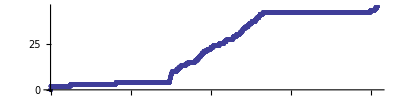
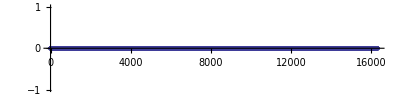
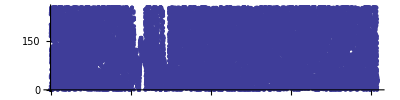
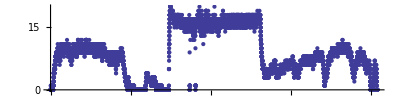
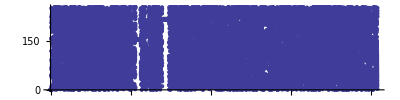
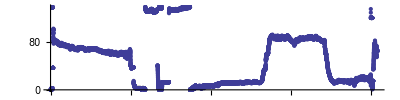
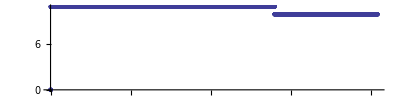
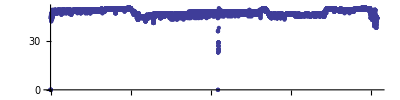
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
"Progress"
min=50;
max=350;
dat=Transpose[reframed];
ProgressIndicator[Dynamic[k],{min,max}]
TableForm[Transpose[{Table[k=i ;
ListPlot[Flatten[dat[[i]]],PlotRange->All,AspectRatio->0.25],{i,min,max}]}]]
```

```mathematica
Image[reframed,"Byte"]
```

-Graphics-

```mathematica
list=a;
res={};
count=0;
"Progress"
ProgressIndicator[Dynamic[n],{1,Length[list]}]
Do[n=i;
If[list[[i]]==0,count=count+1,If[count≥32,res=Append[res,i-count]];count=0];
,{i,1,Length[list]}
];
n=1;
cuts=Most[Transpose[{res,RotateLeft[res]-1}]];
n=Length[list]/2;
raw=Map[Take[list,#]&,cuts];
reframed=PadRight[raw,Automatic,0];
n=Length[list];
```

Progress

```mathematica
float=Compile[{{a, _Integer},{b, _Integer},{c, _Integer},{d, _Integer}}, 

(1-2*Quotient[a,128])*

(2^(2*Mod[a,128]+Quotient[b,128]-127))*

(256*(256*Mod[b,128]+Mod[c,256])+Mod[d,256])

];
```

```mathematica
float[191,128,1,1]
```

-257

```mathematica
Map[Length,raw]
```

{323,190,190,441,400,421,379,400,427,400,400,421,400,405,418,400,400,400,400,430,440,433,400,400,400,418,409,400,400,379,421,397,409,400,400,421,400,418,409,379,400,400,421,418,409,400,400,400,«16219»,400,400,400,400,400,400,400,400,427,400,400,400,400,427,400,400,400,400,427,400,400,400,400,427,400,400,400,409,418,400,400,400,409,418,443,400,400,409,418,400,400,400,409,418,400,400,400,387}